```mathematica
EmpiricalSitesPerClusterSize[p_,L_]:=Module[{array=Table[If[RandomReal[]<p,1,0],{i,L}]},Counts[Flatten[#/. {1->Length[#]}&/@Split[array]]]]
```

```mathematica
EmpiricalSitesPerClusterSize[.7,10000]
```

<|0→3027,1→644,3→918,2→842,7→483,4→860,14→112,12→216,5→780,8→472,6→630,9→279,11→198,13→117,10→200,16→112,23→23,17→34,19→38,15→15|>

```mathematica
EmpiricalClusterSizeFrecuency[p_,L_]:=ResourceFunction["ToAssociations"][Flatten[KeyValueMap[{#1->#2/#1}&,KeyDrop[EmpiricalSitesPerClusterSize[p,L],0]]]]
```

```mathematica
EmpiricalClusterSizeFrecuency[.3,100000]
```

<|1→14645,2→4480,3→1355,6→29,5→114,4→390,7→16,9→1,8→7,10→1|>

```mathematica
EmpiricalSitesPerClusterSize[.3,100000]
```

<|3→3759,0→70160,2→8822,1→14769,4→1628,6→156,5→580,8→24,9→18,7→84|>

```mathematica
EmpiricalClusterNumberDensity[p_,L_]:=ResourceFunction["ToAssociations"][Flatten[KeyValueMap[{#1->#2/#1}&,KeyDrop[EmpiricalSitesPerClusterSize[p,L],0]/L]]]
```

```mathematica
EmpiricalClusterNumberDensity[.3,100000]
```

<|3→131/10000,2→4517/100000,1→14527/100000,4→49/12500,5→17/12500,6→7/20000,7→1/12500,8→1/50000,9→1/20000|>

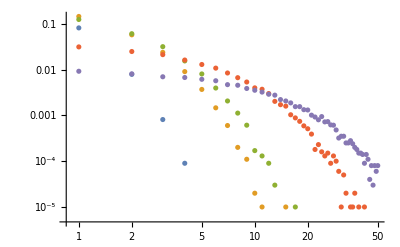

```mathematica
P1=ListLogLogPlot[Table[Table[{x,EmpiricalClusterNumberDensity[P,100000][x]},{x,0,50}],{P,{.1,.4,.5,.8,.9}}]]
```

```mathematica
ClusterNumberDensity[s_,p_]:=(1-p)^2p^s
```

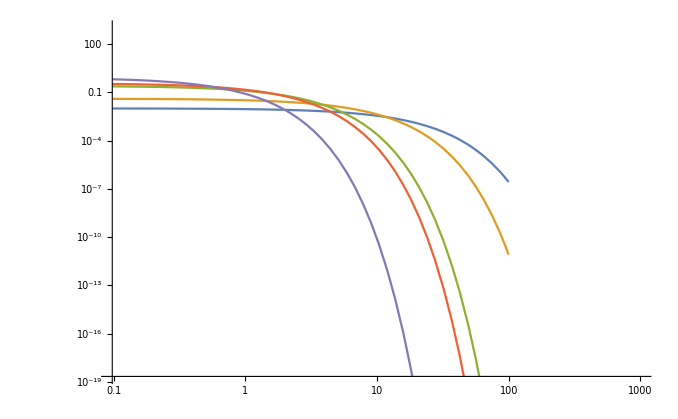

```mathematica
P2=LogLogPlot[Evaluate@Table[ClusterNumberDensity[s,P],{P,{.9,.8,.5,.4,.1}}],{s,0,100},PlotRange->{{0,1000},{0,1000}}]
```

```mathematica
Table[ClusterNumberDensity[s,.9],{P,{.1,.4,.5,.8,.9}}]
```

{0.01 0.9^s,0.01 0.9^s,0.01 0.9^s,0.01 0.9^s,0.01 0.9^s}

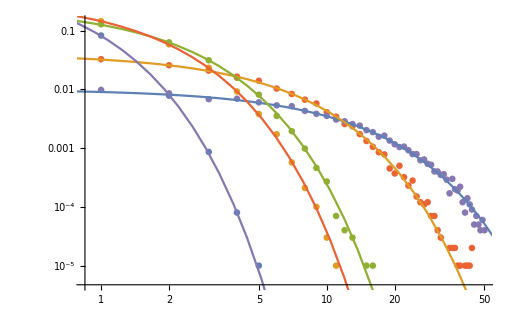

```mathematica
Show[P1,P2]
```

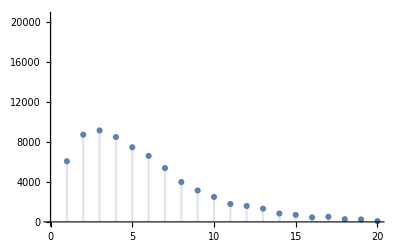

```mathematica
P3=DiscretePlot[EmpiricalSitesPerClusterSize[.7,100000][x],{x,0,20}]
```

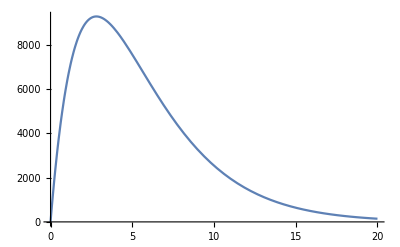

```mathematica
P4=Plot[s 100000(1-.7)^2 .7^s,{s,0,20}]
```

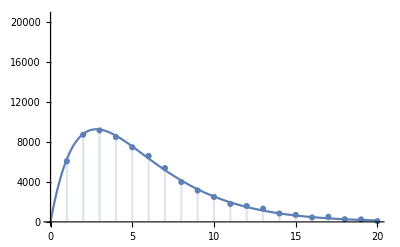

```mathematica
Show[P3,P4]
```